```mathematica
(*Fixed Points and Chemical Potential*)



Num=100; (*# of atoms*)
gr=25.0(*25.0*);
uf=0.3;
ub=0.6;
m=1.0;
kr=14.5;
(*Define the constants*)
α[x_,k_]:=(m*k*x)/(2*π^2)-(2*m*x)^(3/2)/(4*π^2)ArcTan[k/(√(2*m*x))];

β[x_]:=(2*m*x)^(3/2)/(128*π)*Num;
γ[x_,k_]:=(m*k*x)/(2*π^2)+x/uf;

κ[x_]:=gr^2/(32*π)*(2*m*x)^(3/2)/x^2;
λ[x_,ν_]:=(ν+x)/(32*π)*(2*m*x)^(3/2)/x;
σ[x_]:=x/gr;

ξsq[x_,k_]:=x^2*((m (-2 k m x+√2 √(m x) (k^2+2 m x) ArcTan[k/(√2 √(m x))]))/(4 π^2 x (k^2+2 m x)));

ζ[x_,ν_,k_]:=λ[x,ν]/(κ[x]*γ[x,k]);
η[x_,ν_,k_]:=ζ[x,ν,k]/(1+ζ[x,ν,k]);

χ[x_]:=(ub*σ[x]^2)/(32*π)*(2*m*x)^(3/2)/x*Num;
```

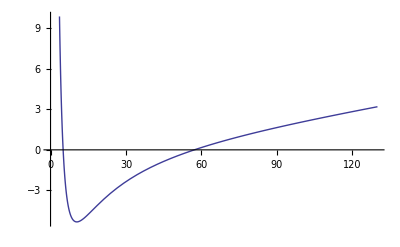

5.00893

```mathematica
ν=-80;

Plot[1+(2 σ[x]^2*λ[x,ν])/χ[x]*(1+(ξsq[x,kr] γ[x,kr]^2)/(2*σ[x]^2*(γ[x,kr]-α[x,kr])^2))*(1+(κ[x]*γ[x,kr])/(2*λ[x,ν]*(γ[x,kr]-α[x,kr]))),{x,0,130}]
FindRoot[1+(2 σ[x]^2*λ[x,ν])/χ[x]*(1+(ξsq[x,kr] γ[x,kr]^2)/(2*σ[x]^2*(γ[x,kr]-α[x,kr])^2))*(1+(κ[x]*γ[x,kr])/(2*λ[x,ν]*(γ[x,kr]-α[x,kr]))),{x,1.0}][[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

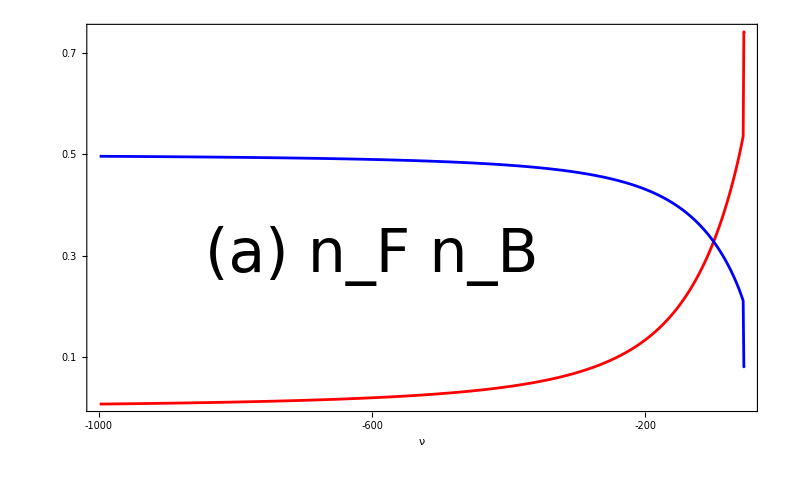

1.

```mathematica
νinit=-1000.0;
νfinal=-56;
νincr=1.0;
Fermi1=Table[ν,{ν,νinit, νfinal,νincr}];
Bose1=Fermi1;
L=Length[Fermi1]+1;
For[i=1,i≤ L-1,i++,
ν=νinit+i*νincr;
e=FindRoot[1+(2 σ[e]^2*λ[e,ν])/χ[e]*(1+(ξsq[e,kr] γ[e,kr]^2)/(2*σ[e]^2*(γ[e,kr]-α[e,kr])^2))*(1+(κ[e]*γ[e,kr])/(2*λ[e,ν]*(γ[e,kr]-α[e,kr]))),{e,1001}][[1]][[2]];
ΨBsq=Abs[λ[e,ν]]/χ[e]*(1+(κ[e]*γ[e,kr])/(2*λ[e,ν]*(γ[e,kr]-α[e,kr])));
ΨFsq=γ[e,kr]/(γ[e,kr]-α[e,kr])*ΨBsq;

Fermi1[[i]]= {ν,ξsq[e,kr]*ΨFsq};
Bose1[[i]]={ν,σ[e]^2*ΨBsq};

];
Fermi1plot=ListPlot[Fermi1,Joined->True,Frame->True,Axes->False,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2],RGBColor[1,0,0]},FrameTicksStyle->Thick];
Fermi1label=Graphics[Text[Style["(a) n_F n_B",FontSize->60],{-600,0.3}]];
Bose1plot=ListPlot[Bose1,Joined->True,Frame->True,Axes->False,FrameLabel->None,RotateLabel->False,PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,1]}];
n100=Show[Fermi1plot,Bose1plot,Fermi1label,PlotRange->All,FrameTicks-> {{{0.1,0.3,0.5,0.7},None},{{-1000,-600,-200,0,100},None}},FrameTicksStyle->Thickness[0.01]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {e} = {1001.`}.

Part::partd: Part specification (-190.69534761209255`) ⟦ 2 ⟧ is longer than depth of object.

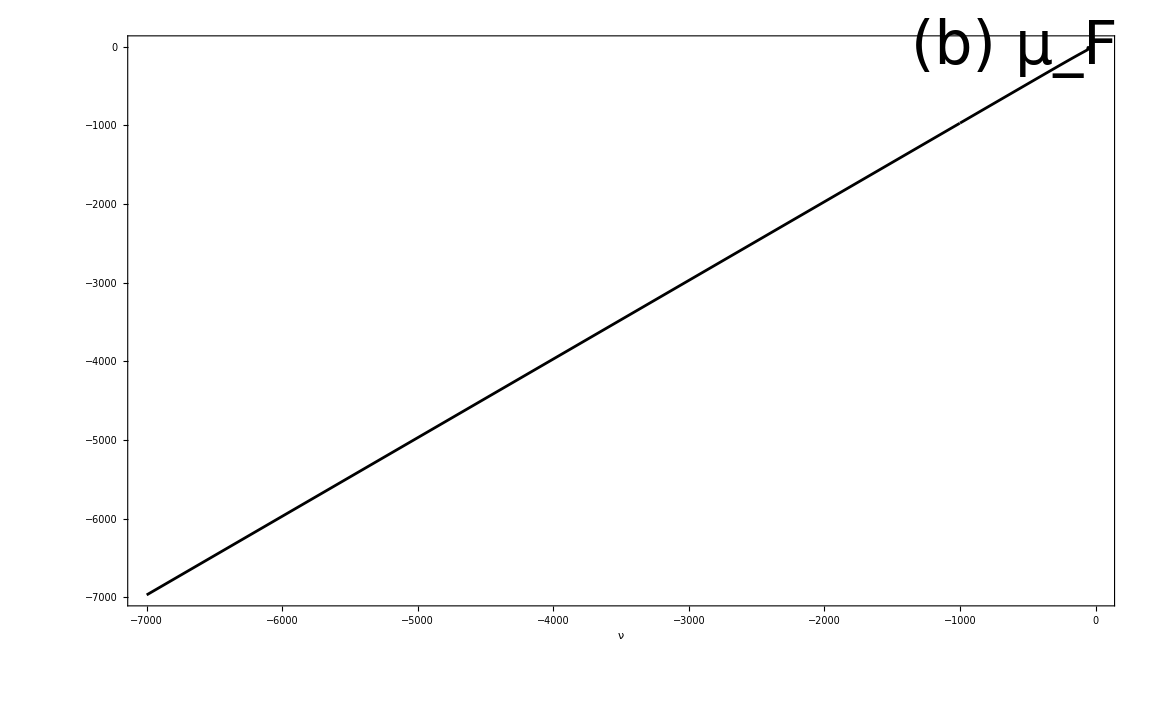

```mathematica
Data1=Table[{ν,(-FindRoot[1+(2 σ[e]^2*λ[e,ν])/χ[e]*(1+(ξsq[e,kr] γ[e,kr]^2)/(2*σ[e]^2*(γ[e,kr]-α[e,kr])^2))*(1+(κ[e]*γ[e,kr])/(2*λ[e,ν]*(γ[e,kr]-α[e,kr]))),{e,1001}][[1]][[2]])},{ν,-20,-7000.0,-1.0}];
p1=ListPlot[Data1,Joined->True,Axes->False,Frame->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,0]},FrameTicksStyle->Thick];
p1label=Graphics[Text[Style["(b) μ_F",FontSize->60],{-600,-20}]];
p100=Show[p1,p1label,FrameTicksStyle->Thickness[0.01]]
```

```mathematica
(*Fixed Point Analysis via Jacobian*)

rbar[x_,ν_,k_]:=√(-λ[x,ν]/χ[x](1+(κ[x]γ[x,k])/(2λ[x,ν](γ[x,k]-α[x,k]))));

DetMu=Data1;
DataSize=Length[DetMu];

BCoeff[x_,ν_,k_]:=(α[x,k]-γ[x,k])^2-((-3+η[x,ν,k])/(-1+η[x,ν,k])*κ[x]*γ[x,k]-2 χ[x]^2  *rbar[x,ν,k]) ((1+η[x,ν,k])/(-1+η[x,ν,k])*κ[x]*γ[x,k]+6 χ[x]^2 *rbar[x,ν,k]);


CCoeff[x_,ν_,k_]:= γ[x,k]^4 *κ[x]^2+(α[x,k]-γ[x,k])^2* ((-3+η[x,ν,k])/(1+η[x,ν,k])*κ[x]*γ[x,k]-2 χ[x]^2 *rbar[x,ν,k]) ((-1+η[x,ν,k])/(1+η[x,ν,k])*κ[x]*γ[x,k]+6 χ[x]^2*rbar[x,ν,k])+2* (κ[x]*γ[x,k]+2 χ[x]^2 *rbar[x,ν,k])* κ[x]*γ[x,k]^2*(α[x,k]-γ[x,k]);




Disc[x_,ν_,k_]:=1+ (4*CCoeff[x,ν,k])/BCoeff[x,ν,k]^2;

Evalsreim01=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Re,√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim02=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{-√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Re,-√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim03=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Re,√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim04=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{-√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Re,-√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];

BData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{ν,BCoeff[ef,ν,kr]},{i,1,DataSize}];
DiscData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{Abs[ν],Disc[ef,ν,kr]},{i,1,DataSize}];
NegDiscData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{Abs[ν],-Disc[ef,ν,kr]},{i,1,DataSize}];
```

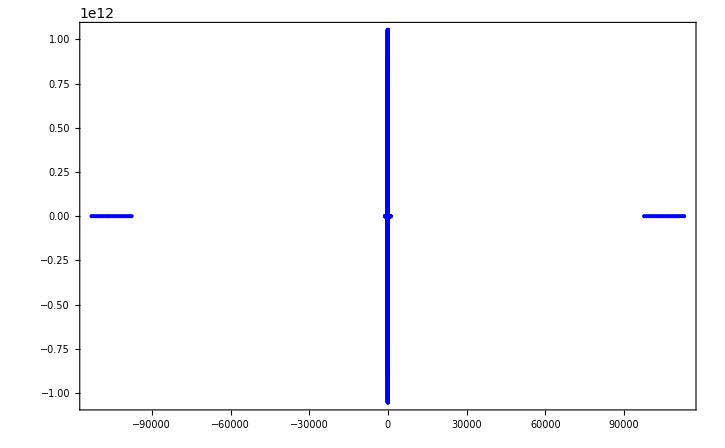

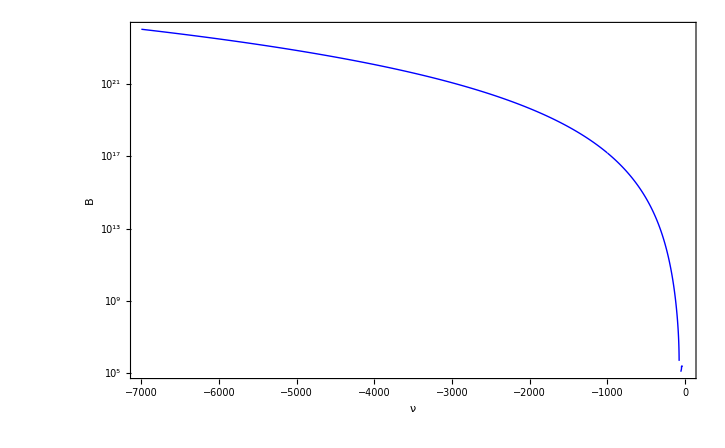

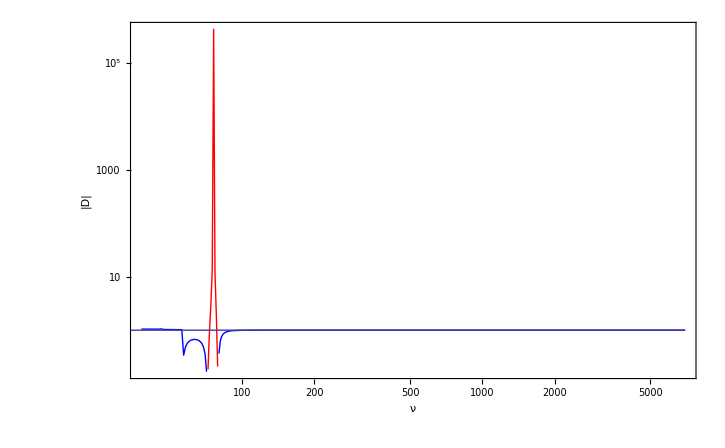

```mathematica
bif=ListPlot[Join[Evalsreim01,Evalsreim02,Evalsreim03,Evalsreim04],Axes->True,Frame->True,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,1]},PlotRange->All];
Show[bif,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]

bplot=ListLogPlot[BData,Axes->True,Frame->True,Joined->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["B",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,PlotStyle->{AbsoluteThickness[1],RGBColor[0,0,1]}];
zero=Plot[0,{ν,DetMu[[1,1]],DetMu[[DataSize,1]]}];
Show[bplot,zero,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]

logplot=ListLogLogPlot[{DiscData,NegDiscData},Axes->True,Frame->True,Joined->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" |D| ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,PlotRange->All,PlotStyle->{Blue,Red},PlotRange->All];
unity=LogLogPlot[1,{ν,DetMu[[1,1]]//Abs,DetMu[[DataSize,1]]//Abs}];
Show[logplot,unity,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```

```mathematica
(*Dynamics*)

ν=-110.0;
ϵ=FindRoot[1+(2 σ[e]^2*λ[e,ν])/χ[e]*(1+(ξsq[e,kr] γ[e,kr]^2)/(2*σ[e]^2*(γ[e,kr]-α[e,kr])^2))*(1+(κ[e]*γ[e,kr])/(2*λ[e,ν]*(γ[e,kr]-α[e,kr]))),{e,1001}][[1]][[2]];
Print["ν = ",ν]
Print["ϵ_F = ",ϵ]
Α=α[ϵ,kr];
Print["α = ",Α]
X=β[ϵ];
Print["χ = ",X]
Γ=γ[ϵ,kr];
Print["γ = ",Γ]
Κ=κ[ϵ];
Print["κ = ",Κ]
Λ=λ[ϵ,ν];
Print["λ = ",Λ]
```

ν = -110.

ϵ_F = 85.4888

α = 15.3988

χ = 555.967

γ = 347.761

κ = 1.90183

λ = -6.37624

```mathematica
tstart=0.001;
tend=0.03;
tendnum=2000.0;
sol=NDSolve[{x'[t]+I*Γ*(x[t]-y[t])-I*Α*x[t]==0,y'[t]+2*I*Λ*y[t]+2*I*X*Abs[y[t]]^2*y[t]-I*Κ*Γ*(x[t]-y[t])==0,x[0]==y[0]==gr/(√2*ϵ)},{x,y},{t,0,tendnum},MaxSteps->20000000];
ψsq[t_]:=10^2*Evaluate[Abs[y[t]]^2/.sol];
```

$Aborted

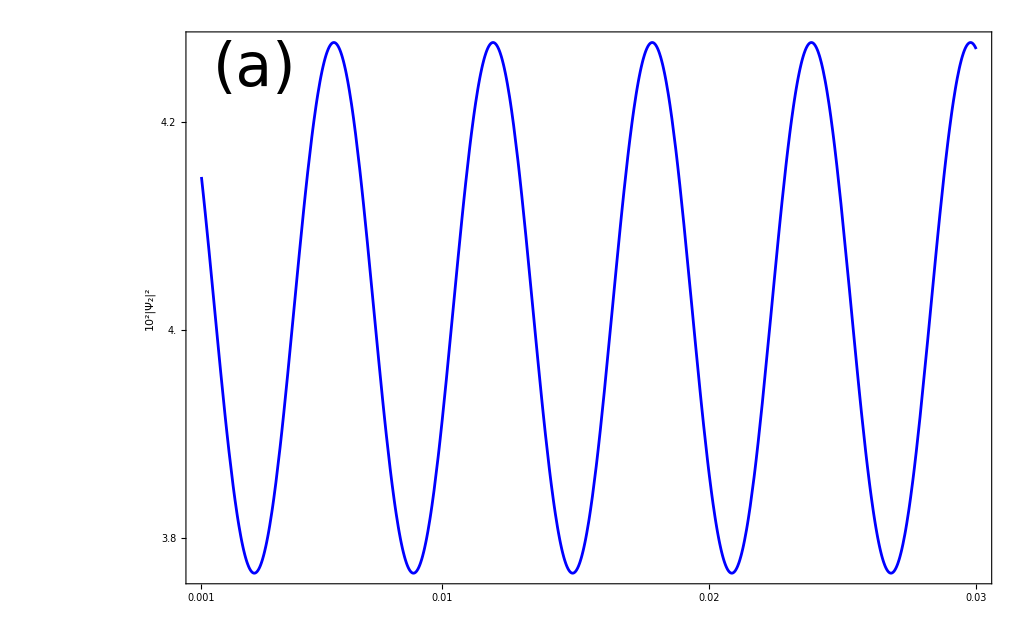

```mathematica
(*Small times*)
ψsq[t_]:=10^2*Evaluate[Abs[y[t]]^2/.sol];
psq1=Plot[ψsq[t],{t,tstart,0.03},PlotRange->All,Frame->True,Axes->False,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicks-> {{{3.8,4.0,4.2,4.4},None},{{0.001,0.01,0.02,0.03},None}},FrameTicksStyle->Thickness[0.01]];
psq1label=Graphics[Text[Style["(a)",FontSize->60],{0.003,4.25}]];
Show[psq1,psq1label]
```

```mathematica
(*Average out the small oscillations*)
t1=0.006;
t2=0.012;
tpm=t2-t1;
Subscript[Ω, m]=(2π)/tpm;(*Small oscillation frequency*)

Print["Small Oscillation Frequency Ω_m = ",Subscript[Ω, m]]
```

Small Oscillation Frequency Ω_m = 1047.2

Small Oscillation Frequency Ω_m = 1047.2

Small Oscillation Frequency Ω_m = 687.363

Small Oscillation Frequency Ω_m = 981.748

Small Oscillation Frequency Ω_m = 1079.59

Small Oscillation Frequency Ω_m = 1079.59

Small Oscillation Frequency Ω = 1079.59

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = (2 π)/tp

Small Oscillation Frequency Ω = 1401.56

Small Oscillation Frequency Ω = 1401.56

Small Oscillation Frequency Ω = 1401.56

«3 more identical outputs»

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 3477.14

Small Oscillation Frequency Ω = 1396.26

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1395.33

Small Oscillation Frequency Ω = 1408.47

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1395.33

Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 3514.09
Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 1408.47
(*Small Oscillation Frequency Ω = 1408.47*)

```mathematica
Envelope=Table[{t,ψsq[t][[1]]},{t,0,2000.0,tpm}];
EnvPlot=ListPlot[Envelope,Joined->True,
PlotRange->All,Frame->True,Axes->False,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicks->{{{3.8,4.0,4.2,4.4},None},{{400,800,1200,1600,2000},None}},FrameTicksStyle->Thickness[0.01]];
EnvLabel=Graphics[Text[Style["(c)",FontSize->60],{380,4.26}]];
Show[EnvPlot,EnvLabel]
```

-Graphics-

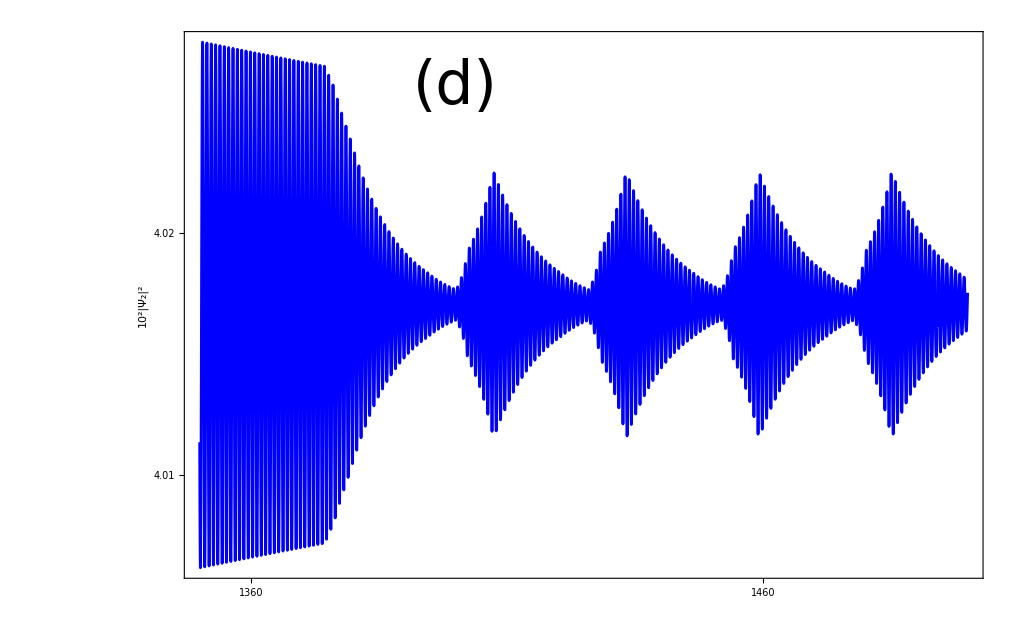

Larger Oscillation Frequency Ω = 10.324

Larger Oscillation Frequency Ω = 10.1834

```mathematica
(*SO THERE IS ANOTHER OSCILLATION!!!!!*)
(*Keep plotting it*)


Envelope=Table[{t,ψsq[t][[1]]},{t,1350,1500.0,tpm}];
EnvPlot=ListPlot[Envelope,Joined->True,Frame->True,PlotRange->All,Axes->False,FrameLabel-> {Style["",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},
FrameTicks-> {{{4.01,4.02,4.03},None},{{1360,1460},None}},FrameTicksStyle->Thickness[0.01]];
EnvLabel=Graphics[Text[Style["(d)",FontSize->60],{1400,4.026}]];
Show[EnvPlot,EnvLabel]
```

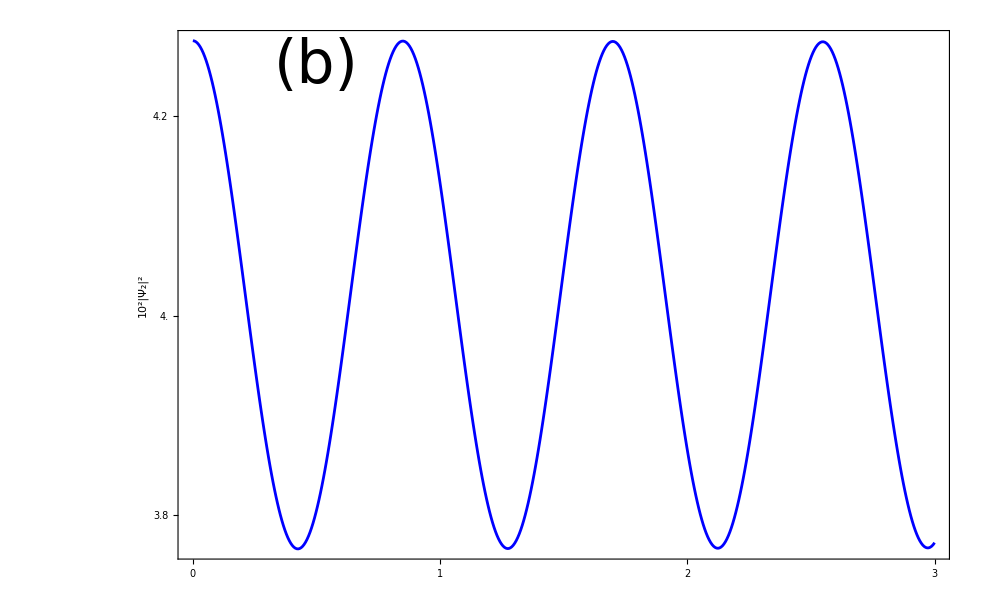

```mathematica
Envelope=Table[{t,ψsq[t][[1]]},{t,0,3.0,tpm}];
EnvPlot=ListPlot[Envelope,Joined->True,
PlotRange->All,Frame->True,Axes->False,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicks->{{{3.8,4.0,4.2,4.4},None},{{0,1,2,3},None}},FrameTicksStyle->Thickness[0.01]];
EnvLabel=Graphics[Text[Style["(b)",FontSize->60],{0.5,4.25}]];
Show[EnvPlot,EnvLabel]
```

```mathematica
(*Calculation of relaxation and revival times*)
ψmax=4.027;
ψmin=4.007;
ψavg=(ψmax+ψmin)/2.0;
ψdif=(ψmax-ψmin)/2.0;
ψrelax=ψdif/2.7818281828459045235;
ψatrelax=ψrelax+ψavg;
Print["Amplitude at t_r=",ψatrelax]
tR=8.0;
Print["Revival time t_R=",tR]
trelaxbegin=1374;
trelaxend=1386;
Print["Relaxation time t_r=",trelaxend-trelaxbegin]
```

Amplitude at t_r=4.02059

Revival time t_R=8.

Relaxation time t_r=12